# Wehrens-Krah: Formidable Figures and Formulas

This notebook contains the necessary functions to create figures from Wehrens & Krah: “Dynamical regulation in bacterial cells during steady state growth”.

Nomenclature: 
 y: CRP reporter
 c: the entire catabolic sector (all CRP-regulated proteins)
 h: constitutive reporter
 
 λ0: mean growth rate 
 λE: effective timescale of metabolic cross-correlations, λE = λ0 (1- T_CM T_MC), T_MC = T_R + T_Mπ -T_Mλ
 L : parameter that summarizes different version of the model: L = -α1 (TR + α2 TMπ). Mostly α1, α2 = 0 is used.

!!! TO LOAD DATA adjust this to your machine’s setting:

```mathematica
dirstring = "\\" ;(*which directoy string used (\\ on windows, / on linux);*)

SetDirectory[NotebookDirectory[]];
λR = {TMC-> TR+TMπ-TMλ,λE-> λ0(1-TCM(TR + TMπ-TMλ))};

SetOptions[Plot,{PlotRange->All,PlotStyle-> {{AbsoluteThickness[5]},{AbsoluteThickness[2],Dashed}},Frame-> True,FrameStyle-> Thick,LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],ImageSize-> 400,AspectRatio-> .9}];
```

## Preparing the model and the data

## Defining Functions

### Cross-Covariance Functions

#### Analytical Component functions

```mathematica
A[t_,β_, θ_,λi_]:=(θ^2 λ0)/(2 β)Piecewise[{{ⅇ^(-β t)/(β+λi),t≥ 0},{(2 β ⅇ^(λi t))/(β^2-λi^2)-ⅇ^(β t)/(β-λi),t<0}}];
B[t_,β_, θ_]:=θ^2/(2 β)ⅇ^(- β Abs[t]);
S[t_,β_, θ_]:=(θ^2 λ0^2)/(2 (β^2-λE^2))(ⅇ^(-λE Abs[t])/λE- ⅇ^(-β Abs[t])/β);

D1[t_,β_, θ_]:=(θ^2 λ0^2)/2 Piecewise[{{(2 ⅇ^(-λE t))/((β^2-λE^2)(λ0+λE))-ⅇ^(-β t)/(β(β+λ0)(β-λE)),t≥ 0},{(2 ⅇ^(λ0 t))/((β^2-λ0^2)(λ0+λE))-ⅇ^(β t)/(β(β+λE)(β-λ0)),t<0}}];
D2[t_,β_, θ_]:=(θ^2 λ0^2)/2 Piecewise[{{ⅇ^(-β t)/(β(β+λE)(β+λ0)),t≥ 0},{ⅇ^(β t)/(β(β- λ0)(β-λE))+2/(λ0-λE)(ⅇ^(λE t)/(β^2-λE^2)-ⅇ^(λ0 t)/(β^2-λ0^2)),t<0}}];
D3[t_,β_, θ_]:=(θ^2 λ0^3)/2 Piecewise[{{ⅇ^(-λE t)/(λE(λ0+λE)(β^2-λE^2))-ⅇ^(-β t)/(β(β+λ0)(β^2-λE^2)),t≥ 0},{ ⅇ^(t β)/(β (β-λ0) (β^2-λE^2))-(2 ⅇ^(t λ0))/((β^2-λ0^2) (λ0^2-λE^2))+ⅇ^(t λE)/(λE (λ0-λE) (β^2-λE^2)),t<0}}];
```

Specific functions for Nπc

```mathematica
A0πc[t_]:=A[t,βπc,θπc,λ0];
Aπc[t_]:=A[t,βπc,θπc,λE];
Sπc[t_]:= S[t,βπc,θπc];
D1πc[t_]:= D1[t,βπc,θπc];
D2πc[t_]:=D2[t,βπc,θπc];
D3πc[t_]:=D3[t,βπc,θπc];
```

Specific functions for Ns

```mathematica
A0s[t_]:=A[t,βs,θs,λ0];
As[t_]:=A[t,βs,θs,λE]; 
Ss[t_]:= S[t,βs,θs];
Bs[t_]:=B[t,βs,θs]; 
D1s[t_]:= D1[t,βs,θs];
D2s[t_]:=D2[t,βs,θs];
D3s[t_]:=D3[t,βs,θs];
```

Specific functions for Nπy

```mathematica
Aπy[t_]:=A[t,βπy,θπy,λE];
A0πy[t_]:=A[t,βπy,θπy,λ0];
Sπy[t_]:= S[t,βπy,θπy];
D1πy[t_]:= D1[t,βπy,θπy];
D2πy[t_]:=D2[t,βπy,θπy];
D3πy[t_]:=D3[t,βπy,θπy];
```

Specific functions for Nπh

```mathematica
Aπh[t_]:=A[t,βπh,θπh,λE];
A0πh[t_]:=A[t,βπh,θπh,λ0];
Sπh[t_]:= S[t,βπh,θπh];
D1πh[t_]:= D1[t,βπh,θπh];
D2πh[t_]:=D2[t,βπh,θπh];
D3πh[t_]:=D3[t,βπh,θπh];
```

Specific functions for Nλ

```mathematica
Aλ[t_]:=A[t,βλ,θλ,λE];
A0λ[t_]:=A[t,βλ,θλ,λ0];
Sλ[t_]:= S[t,βλ,θλ];
D1λ[t_]:= D1[t,βλ,θλ];
D2λ[t_]:=D2[t,βλ,θλ];
D3λ[t_]:=D3[t,βλ,θλ];
```

Specific functions for NM

```mathematica
AM[t_]:=A[t,βM,θM,λE];
A0M[t_]:=A[t,βM,θM,λ0];
SM[t_]:= S[t,βM,θM];
BM[t_]:= B[t,βM,θM];
D1M[t_]:=D1[t,βM,θM];
D2M[t_]:=D2[t,βM,θM];
D3M[t_]:=D3[t,βM,θM];
```

#### Cross-covariances (Decomposed)

Split functions up in their modes: 1) Control, 2) Dilution, 3) Metabolism/Common, 4) Regulation

CRP-sector and growth (λ)

```mathematica
χMϕcλ[t_,MODES_]:=
MODES⟦1⟧(TCM TMλ(Sπc[t] + Ss[t] ))+
MODES⟦2⟧(-Aλ[t]) +
MODES⟦3⟧((TMπ-TMλ) TMλ AM[t]+TCM TMλ(TMC^2 SM[t] + Sλ[t]))+
MODES⟦4⟧(TR TMλ AM[t]);

χMπcλ[t_,MODES_]:=
MODES⟦1⟧( TCM TMλ(Aπc[-t] + As[-t]))+
MODES⟦2⟧(0)+
MODES⟦3⟧(TMπ TMλ  BM[t]-TCM TMπ Aλ[t] +(TCM TMλ)(TCM TMπ)(Sπc[t] + Ss[t] + TMC^2 SM[t]+Sλ[t])+2 λE/λ0(TMC TCM TMπ)TMλ  SM[t] )+
MODES⟦4⟧(TR TMλ  BM[t]-TCM TR Aλ[t] +(TCM TMλ)(TCM TR )(Sπc[t] + Ss[t] + TMC^2 SM[t]+Sλ[t])2 λE/λ0(TMC TCM TR)TMλ  SM[t]);
```

CRP-reporter (Y) and and growth (λ)

```mathematica
χMϕyλ[t_,MODES_]:=
MODES⟦1⟧( TCM TMλ D1s[t])+
MODES⟦2⟧(-A0λ[t])+
MODES⟦3⟧((TMπ- TMλ) TMλ A0M[t]+TCM TMC (TMC TMλ D2M[t]-D2λ[t]) + (TCM (TMπ - TMλ)) (TCM TMλ)(D3πc[t] + D3s[t] + TMC^2 D3M[t] + D3λ[t])   +(TMC TCM (TMπ - TMλ))  TMλ D1M[t] +(TCM TMλ) D1λ[t])+
MODES⟦4⟧(TR TMλ A0M[t] + (TCM TR) (TCM TMλ)(D3πc[t] + D3s[t] + TMC^2 D3M[t] + D3λ[t])   +(TCM TMC TR )( TMλ)D1M[t] ) ;

χMπyλ[t_,MODES_]:= 
MODES⟦1⟧(TCM TMλ As[-t])+
MODES⟦2⟧(0)+
MODES⟦3⟧(TMπ TMλ  BM[t]+(TCM TMπ )(TCM TMλ)(Sπc[t] + Ss[t] + TMC^2 SM[t] + Sλ[t])+ 2 λE/λ0 TMπ(TMC TCM  TMλ)  SM[t] -(TCM TMπ) Aλ[t])+
MODES⟦4⟧(TR TMλ  BM[t]+(TCM TR )(TCM TMλ)(Sπc[t]+Ss[t]+TMC^2 SM[t]+Sλ[t])+2 λE/λ0 TR(TMC TCM  TMλ)  SM[t]-(TCM TR) Aλ[t] );
```

Constitutive (H) and growth (λ) are removed because of the added resource competition (α1), clouding the interpretation of the modes.

#### Analytical Cross-covariances (Composed)

CRP-sector and growth (λ)

```mathematica
χϕcλ[t_]:=-Aλ[t] + TMC TMλ  AM[t] + TCM TMλ(Sπc[t] + Ss[t] + TMC^2 SM[t] + Sλ[t]);
χπcλ[t_]:=-TCM (TR+ TMπ)Aλ[t] + 2 λE/λ0 TMC TCM (TR+ TMπ)TMλ  SM[t] + TCM TMλ(Aπc[-t] + As[-t])+TCM^2 TMλ(TR + TMπ)(Sπc[t] + Ss[t] + TMC^2 SM[t]+Sλ[t]) + TMλ(TR+ TMπ)BM[t]
```

CRP-reporter (Y) and and growth (λ)

```mathematica
χϕyλ[t_]:= -A0λ[t] + TMC TMλ A0M[t] + TCM TMλ(D1s[t]+TMC^2 D1M[t] + D1λ[t]) + TCM TMC (TMC TMλ D2M[t]-D2λ[t] ) + TCM^2 TMC TMλ(D3πc[t] + D3s[t] + TMC^2 D3M[t] + D3λ[t])
χπyλ[t_]:= TMλ(TR+ TMπ)BM[t] + 2 λE/λ0 TCM TMC TMλ(TR+ TMπ) SM[t]+TCM (TMλ As[-t] -(TR+ TMπ)Aλ[t])+TCM^2(TR+ TMπ)TMλ(Sπc[t] + Ss[t] + TMC^2 SM[t] + Sλ[t]);
```

Constitutive (H) and growth (λ)

```mathematica
χϕhλ[t_]:=(TMπh-L-TMλ)TMλ A0M[t] - A0λ[t] + TCM TMλ((TMπh-L-TMλ)TMC D1M[t] + D1λ[t]) + TCM(TMπh-L-TMλ)(TMC TMλ D2M[t] - D2λ[t]) + TCM^2(TMπh-L-TMλ)TMλ(D3πc[t] + D3s[t] + TMC^2 D3M[t] + D3λ[t])-α1 TCM TMλ D1s[t];

χπhλ[t_]:=(TMπh-L) TMλ BM[t] + 2 λE/λ0(TMπh-L)(TMC TCM TMλ)SM[t] - TCM (TMπh-L) Aλ[t] + TCM^2(TMπh-L) TMλ (Sπc[t] + Ss[t] + TMC^2 SM[t]+Sλ[t])-α1 TCM TMλ As[-t]
```

Production Rates πH and πY

```mathematica
χπhπy[t_]:=(TR+TMπ)(TMπh-L) BM[t]+ TCM (TMπh-L) As[t] + TMC TCM (TMπh-L)(TR+ TMπ)2 λE/λ0 SM[t] + TCM^2 (TMπh-L) (TMπ+TR)(Ss[t] + TMC^2 SM[t] + Sλ[t])-α1 Bs[t]-α1 TCM(TR+TMπ)As[-t]
```

### Variance Functions

CRP-sector

```mathematica
η2ϕC=λ0^2/(2 λE)(θπc^2/(βπc (βπc+λE))+ θs^2/(βs(βs+λE))+TMC^2 θM^2/(βM(βM+λE))+θλ^2/(βλ(βλ+λE)));

η2πC=θπc^2/(2 βπc)(1+ (2 λ0)/(βπc + λE) TCM (TR + TMπ)) + θs^2/(2 βs)(1+ (2λ0)/(βs + λE) TCM (TR+ TMπ)) + θM^2/(2 βM)(TR + TMπ)^2(1+ (2 λ0)/(βM + λE)TCM TMC) + TCM^2(TR + TMπ)^2 η2ϕC;

η2λ=θλ^2/(2 βλ)(1-(2 λ0)/(βλ+λE)TCM TMλ) +θM^2/(2 βM)TMλ^2(1+ (2λ0)/(βM+λE)TCM TMC) +TCM^2 TMλ^2 η2ϕC;
```

Y-reporter

```mathematica
η2ϕy=θπy^2/(2 βπy)λ0/(βπy + λ0) + θπc^2/(2βπc)λ0/(βπc+λ0)λ0^2 TCM^2 TMC^2 (βπc+λ0 + λE)/((βπc+λE)λE(λ0+λE))+ θs^2/(2 βs) λ0/(βs+λ0)(1+ TCM TMC (λ0(βs + λ0 + λE))/(λE( βs + λE))) + θM^2/(2 βM) λ0/(βM + λ0)TMC^2(1+ TCM TMC (λ0(βM+λ0+λE))/(λE(βM+λE))) + θλ^2/(2βλ)λ0/(βλ+λ0)(1+ TCM TMC (λ0(βλ + λ0+λE))/(λE(βλ+λE))) ;

η2πy=θπy^2/(2 βπy) + θs^2/(2 βs)(1+2 λ0/(βs+λE)TCM (TR + TMπ)) + θM^2/(2 βM)(TR + TMπ)^2(1+2 λ0/(βM+λE) TCM TMC) + TCM^2(TR+ TMπ)^2 η2ϕC;
```

H-reporter

```mathematica
η2ϕh =(θπh^2 λ0)/(2 βπh (βπh+λ0))  +(α1 θs^2 λ0)/(2 βs (βs+λ0))(α1 -TCM(TMπh-L-TMλ)(2λ0(βs+λ0+λE))/((βs+λE) (λ0+λE)))+(λ0^3 TCM^2(TMπh - L-TMλ)^2)/(2 λE(λ0+λE))((θπc^2(βπc + λ0 + λE))/(βπc(βπc+λ0)(βπc+λE)) +(θs^2(βs+λ0+λE))/(βs(βs+λ0)(βs+λE)))+
(θM^2 λ0(TMπh-L- TMλ)^2)/(2 βM(βM+λ0))(1+ TCM TMC (λ0(βM+λ0+λE))/(λE(βM+λE))) + (θλ^2 λ0)/(2 βλ(βλ+λ0))(1+ TCM (TMπh-L-TMλ)(λ0(βλ+λ0+λE))/((βλ+λE)(λ0+λE))(TCM(TMπh-L-TMλ)λ0/λE+2));


η2πh =θπh^2/(2 βπh) +  θs^2/(2 βs)α1(α1-2  λ0/(βs + λE)TCM (TMπh - L))+ θM^2/(2 βM)(TMπh-L)^2(1+ 2 λ0/(βM + λE)  TCM TMC ) + TCM^2( TMπh - L)^2 η2ϕC;
```

### Cross-Correlation Functions

```mathematica
Rϕcλ[t_]:= χϕcλ[t]/(√Abs[η2ϕC η2λ]);
Rπcλ[t_]:= χπcλ[t]/(√Abs[η2πC η2λ]);
Rϕyλ[t_]:= χϕyλ[t]/(√Abs[η2ϕy η2λ]);

Rπyλ[t_]:= χπyλ[t]/(√Abs[η2πy η2λ]);
Rϕhλ[t_]:= χϕhλ[t]/(√Abs[η2ϕh η2λ]);

Rπhλ[t_]:= χπhλ[t]/(√Abs[η2πh η2λ]);
Rπhπy[t_]:=χπhπy[t]/(√Abs[η2πh η2πy]);
```

## Loading Data

### Data Loading and Locating Functions

```mathematica
Needs["ErrorBarPlots`"];
Datalocation = ParentDirectory[]<>dirstring<>"Data"<>dirstring<>"Crosscorrs";
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
styleWAϕ = {Darker[Black]};
styleWAπ = {Darker[Black],Dashed};
joinedlist ={True,False,True,False};
```

CCsdatalist is a list of all experiments,    with each experiment being a list of 3 xT (where T is the time of the experiment), on each time point we have : {time, value, error}). 
  The first step is to make sure all experiments have the same time-length (difficult because different experiments have used different times between measurements,  so linear interpolation is used), then we calculate weighted averaged between the experiments, using the errors^-2 as weights. 
  Finally we prepare these weighted averaged including their calculated errors to be plotted including error bars

```mathematica
(*Used to give all experiments the time of the shortest time series*)

intraval[tx_,list_,i_]:= 
Module[{y1,y2,t1,t2,t0,s1,s2,sx, y,s},
{t1,y1,s1} = list⟦i-1⟧;
{t2,y2,s2} = list⟦i⟧;
 y=y1 + (y2-y1)/(t2-t1)(tx-t1);
s = s1 + (s2-s1)/(t2-t1)(tx-t1);
Return[{tx,y,s}]
];

intralist[list_,times_,t0_,tend_]:=Module[{eqtimelist,i,j,tx},
tx = t0;  eqtimelist = {}; 
For[j=1,j≤ Length[times],j++,
{tx = times⟦j⟧,
For[i = 1,i<Length[list],i++,
If[tx≤  list⟦i,1⟧,
{AppendTo[eqtimelist,intraval[tx,list,i]],
i = Length[list]+1}]]
}
];
Return[eqtimelist]];

EquateLengths[CCsdatalist_]:=
 Module[{pickitime, time,dt,t0, tend,equallist,iloop},
pickitime=Position[-CCsdatalist⟦All,1,1⟧,Min[-CCsdatalist⟦All,1,1⟧]]⟦1,1⟧;
time = CCsdatalist⟦pickitime,All,1⟧;
t0 = time⟦1⟧; tend = time⟦-1⟧;
equallist = {CCsdatalist⟦pickitime⟧};
For[iloop = 1,iloop≤ Length[CCsdatalist⟦All,1,1⟧], iloop++,If[iloop ≠ pickitime, AppendTo[equallist,intralist[CCsdatalist⟦iloop⟧,time,t0,tend]]]];
Return[equallist]
]

WA[CCsdatalist_]:= Module[{returnlist,time, Nw},
Nw = Sum[1/CCsdatalist⟦iexp,All,3⟧^2,{iexp,1,Length[CCsdatalist]}];
time=Sum[CCsdatalist⟦iexp,All,1⟧,{iexp,1,Length[CCsdatalist]}]/Length[CCsdatalist];
returnlist={time,1/Nw Sum[CCsdatalist⟦iexp,All,2⟧/CCsdatalist⟦iexp,All,3⟧^2,{iexp,1,Length[CCsdatalist]}]}ᵀ
];

(* Option 1: weight by σ^2 (ignoring inter-experimental noise)
σA[CCsdatalist_]:= Module[{σreturn,Nw},
Nw = Sum[1/CCsdatalist⟦iexp,All,3⟧^2,{iexp,1,Length[CCsdatalist]}];
σreturn = 1/(√Nw)];*)

σA[CCsdatalist_]:=Module[{nexp,returnlist,Nw,sμ2,si2, μlist,ni,σ2},
nexp = Length[CCsdatalist];
ni = 4;
si2 = CCsdatalist⟦All,All,3⟧ᵀ;
sμ2= Table[Variance[CCsdatalist⟦All,All,2⟧ᵀ⟦i⟧],{i,Length[CCsdatalist⟦All,All,2⟧ᵀ]}];

σ2=(sμ2 Sum[ni^2,{i,1,nexp}]+Sum[ni si2⟦All,i⟧,{i,nexp}])/Sum[ni,{i,1,nexp}]^2;
 Return[√σ2]

];



ErrorPlotPrep[CC_,σ_]:=Module[{Wsum, returnlist,time},
time = CC⟦All,1⟧;
returnlist={Table[{CC⟦itime⟧,ErrorBar[0]},{itime,1,Length[time]}],
Table[{CC⟦itime⟧,ErrorBar[If[σ⟦itime⟧<10^7,σ⟦itime⟧,0]]},{itime,1,Length[time],5}]};
Return[returnlist]]
```

### Loading WT and Optimal Mutant Data

First import WT data

```mathematica
SetDirectory[Datalocation<>dirstring<>"WT_lac"]; 
SetOptions[ListPlot,{PlotRange-> {All,{-.5,.5}},Frame-> True,FrameStyle-> Thick,LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],ImageSize-> 550,AspectRatio-> .9,
Joined-> joinedlist,PlotStyle-> {styleWAϕ,styleWAϕ,styleWAπ,styleWAϕ}}];

name = "WT_" ;(*Set the basal name of these experiments*)
nexp = 6; (*Set the number of experiments done for this strain*)

ϕYμWT = {};
For[iexp = 1, iexp <= nexp, iexp++, AppendTo[ϕYμWT, Import[name <> ToString[iexp] <> "_phiY_mu.dat", "CSV"]];] ; Clear[iexp];
ϕYμWT = EquateLengths[ϕYμWT];

ϕHμWT = {};
For[iexp = 1, iexp <= nexp, iexp++, AppendTo[ϕHμWT, Import[name <> ToString[iexp] <> "_phiH_mu.dat", "CSV"]];]; Clear[iexp];
ϕHμWT = EquateLengths[ϕHμWT];


πYμWT = {};
For[iexp = 1, iexp <= nexp, iexp++, AppendTo[πYμWT, Import[name <> ToString[iexp] <> "_piY_mu.dat", "CSV"]];] ; Clear[iexp];
πYμWT = EquateLengths[πYμWT];

πHμWT = {};
For[iexp = 1, iexp <= nexp, iexp++, AppendTo[πHμWT, Import[name <> ToString[iexp] <> "_piH_mu.dat", "CSV"]];]; Clear[iexp];
πHμWT = EquateLengths[πHμWT];


πHπYWT = {};
For[iexp = 1, iexp <= nexp, iexp++, AppendTo[πHπYWT, Import[name <> ToString[iexp] <> "_piH_piY.dat", "CSV"]];] ; Clear[iexp];
πHπYWT = EquateLengths[πHπYWT];


RϕYλDATA = WA[ϕYμWT]; RπYλDATA = WA[πYμWT];
σϕYλDATA = σA[ϕYμWT]; σπYλDATA = σA[πYμWT];

RϕHλDATA = WA[ϕHμWT]; RπHλDATA = WA[πHμWT];
σϕHλDATA = σA[ϕHμWT]; σπHλDATA = σA[πHμWT]; 

RπHπYDATA = WA[πHπYWT]; 
σπHπYDATA = σA[πHπYWT];
Clear[ϕYμWT, πYμWT, ϕHμWT, πHμWT,πHπYWT, nexp, name];
```

Then, import mutant data

```mathematica
SetDirectory[Datalocation<>dirstring<>"MUT_opt"]; 

name = "MUT_opt_" ;(*Set the basal name of these experiments*)
nexp = 4; (*Set the number of experiments done for this strain*)

ϕYμMUT = {};
For[iexp = 1, iexp <= nexp, iexp++, AppendTo[ϕYμMUT, Import[name <> ToString[iexp] <> "_phiY_mu.dat", "CSV"]];] ; Clear[iexp];
ϕYμMUT = EquateLengths[ϕYμMUT];

ϕHμMUT = {};
For[iexp = 1, iexp <= nexp, iexp++, AppendTo[ϕHμMUT, Import[name <> ToString[iexp] <> "_phiH_mu.dat", "CSV"]];]; Clear[iexp];
ϕHμMUT = EquateLengths[ϕHμMUT];


πYμMUT = {};
For[iexp = 1, iexp <= nexp, iexp++, AppendTo[πYμMUT, Import[name <> ToString[iexp] <> "_piY_mu.dat", "CSV"]];] ; Clear[iexp];
πYμMUT = EquateLengths[πYμMUT];

πHμMUT = {};
For[iexp = 1, iexp <= nexp, iexp++, AppendTo[πHμMUT, Import[name <> ToString[iexp] <> "_piH_mu.dat", "CSV"]];]; Clear[iexp];
πHμMUT = EquateLengths[πHμMUT];

πHπYMUT = {};
For[iexp = 1, iexp <= nexp, iexp++, AppendTo[πHπYMUT, Import[name <> ToString[iexp] <> "_piH_piY.dat", "CSV"]];] ; Clear[iexp];
πHπYMUT = EquateLengths[πHπYMUT];



RϕYλOPTMUTDATA = WA[ϕYμMUT]; RπYλOPTMUTDATA = WA[πYμMUT];
σϕYλOPTMUTDATA = σA[ϕYμMUT]; σπYλOPTMUTDATA = σA[πYμMUT];

RϕHλOPTMUTDATA = WA[ϕHμMUT]; RπHλOPTMUTDATA = WA[πHμMUT];
σϕHλOPTMUTDATA = σA[ϕHμMUT]; σπHλOPTMUTDATA = σA[πHμMUT]; 

RπHπYOPTMUTDATA = WA[πHπYMUT]; 
σπHπYOPTMUTDATA = σA[πHπYMUT];
Clear[ϕYμMUT, πYμMUT, ϕHμMUT, πHμMUT, πHπYMUT, nexp, name];
```

```mathematica
posππpeak[list_] := Flatten[{Position[list[[All, 1]], Sort[Abs[list[[All, 1]]]][[1]]] - 1, Position[list[[All, 1]], Sort[Abs[list[[All, 1]]]][[1]]], Position[list[[All, 1]], Sort[Abs[list[[All, 1]]]][[1]]] + 1}]
σπHπYDATA[[posππpeak[RπHπYDATA]]] = ∞;
σπHπYOPTMUTDATA[[posππpeak[RπHπYOPTMUTDATA]]] = ∞;
```

```mathematica
YWTPlot = ErrorListPlot[Flatten[{ErrorPlotPrep[RϕYλDATA, σϕYλDATA], ErrorPlotPrep[RπYλDATA, σπYλDATA]}, 1], FrameLabel -> {{"" , ""}, {"τ (h)", "WT: Y-λ"}}];
HWTPlot = ErrorListPlot[Flatten[{ErrorPlotPrep[RϕHλDATA, σϕHλDATA], ErrorPlotPrep[RπHλDATA, σπHλDATA]}, 1], FrameLabel -> {{"" , ""}, {"τ (h)", "WT: H-λ"}}];
ππWTPlot = ErrorListPlot[ErrorPlotPrep[RπHπYDATA, σπHπYDATA], FrameLabel -> {{"" , ""}, {"τ (h)", "WT: πH-πY"}}];
YOPTMUTPlot = ErrorListPlot[Flatten[{ErrorPlotPrep[RϕYλOPTMUTDATA, σϕYλOPTMUTDATA], ErrorPlotPrep[RπYλOPTMUTDATA, σπYλOPTMUTDATA]}, 1], FrameLabel -> {{"" , ""}, {"τ (h)", "MUT: Y-λ"}}];
HOPTMUTPlot = ErrorListPlot[Flatten[{ErrorPlotPrep[RϕHλOPTMUTDATA, σϕHλOPTMUTDATA], ErrorPlotPrep[RπHλOPTMUTDATA, σπHλOPTMUTDATA]}, 1], FrameLabel -> {{"" , ""}, {"τ (h)", "MUT: H-λ"}}];
ππOPTMUTPlot = ErrorListPlot[ErrorPlotPrep[RπHπYOPTMUTDATA, σπHπYOPTMUTDATA], FrameLabel -> {{"" , ""}, {"τ (h)", "MUT: πH-πY"}}];

SetDirectory[NotebookDirectory[]];
```

```mathematica
{{YWTPlot, HWTPlot, ππWTPlot},
    {YOPTMUTPlot, HOPTMUTPlot, ππOPTMUTPlot}}ᵀ // TableForm;
```

### Loading Low and High Mutant Data

First import LOW MUT data

```mathematica
SetDirectory[Datalocation<>dirstring<>"MUT_low"]; name1 = "MUT_low_1_"; name2 = "MUT_low_2_";

SetOptions[ListPlot,{PlotRange-> {All,{-.7,.7}},Frame-> True,FrameStyle-> Thick,LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],ImageSize-> 550,AspectRatio-> .9,
Joined-> joinedlist,PlotStyle-> {styleWAϕ,styleWAϕ,styleWAπ,styleWAϕ}}];


ϕYμLOW ={Import[name1<>"phiY_mu.dat", "CSV"], Import[name2<>"phiY_mu.dat","CSV"]};
ϕHμLOW ={Import[name1<>"phiH_mu.dat", "CSV"], Import[name2<>"phiH_mu.dat","CSV"]};

πYμLOW ={Import[name1<>"piY_mu.dat", "CSV"], Import[name2<>"piY_mu.dat","CSV"]};
πHμLOW ={Import[name1<>"piH_mu.dat", "CSV"], Import[name2<>"piH_mu.dat","CSV"]};

πHπYLOW = {Import[name1<>"piH_piY.dat", "CSV"], Import[name2<>"piH_piY.dat","CSV"]};

ϕYμLOW = EquateLengths[ϕYμLOW];
ϕHμLOW = EquateLengths[ϕHμLOW];

πYμLOW = EquateLengths[πYμLOW];
πHμLOW = EquateLengths[πHμLOW];

πHπYLOW = EquateLengths[πHπYLOW];

RϕYλLOWDATA= WA[ϕYμLOW]; RπYλLOWDATA = WA[πYμLOW];
σϕYλLOWDATA = σA[ϕYμLOW];σπYλLOWDATA = σA[πYμLOW];
RϕHλLOWDATA= WA[ϕHμLOW]; RπHλLOWDATA = WA[πHμLOW];
σϕHλLOWDATA = σA[ϕHμLOW];σπHλLOWDATA = σA[πHμLOW];

RπHπYLOWDATA= WA[πHπYLOW];
σπHπYLOWDATA =σA[πHπYLOW];

 Clear[ϕYμLOW,πYμLOW,πHπYLOW,ϕHμLOW,πHμLOW];
```

Then import HIGH MUT data

```mathematica
SetDirectory[Datalocation<>"/MUT_high"]; name1 = "MUT_high_1_"; name2 = "MUT_high_2_";
ϕYμHIGH ={Import[name1<>"phiY_mu.dat", "CSV"], Import[name2<>"phiY_mu.dat","CSV"]};
ϕHμHIGH={Import[name1<>"phiH_mu.dat", "CSV"], Import[name2<>"phiH_mu.dat","CSV"]};

πYμHIGH={Import[name1<>"piY_mu.dat", "CSV"], Import[name2<>"piY_mu.dat","CSV"]};
πHμHIGH={Import[name1<>"piH_mu.dat", "CSV"], Import[name2<>"piH_mu.dat","CSV"]};

πHπYHIGH ={Import[name1<>"piH_piY.dat", "CSV"], Import[name2<>"piH_piY.dat","CSV"]};

ϕYμHIGH = EquateLengths[ϕYμHIGH];
ϕHμHIGH = EquateLengths[ϕHμHIGH];

πYμHIGH = EquateLengths[πYμHIGH];
πHμHIGH = EquateLengths[πHμHIGH];

πHπYHIGH = EquateLengths[πHπYHIGH];

RϕYλHIGHDATA= WA[ϕYμHIGH]; RπYλHIGHDATA = WA[πYμHIGH];
σϕYλHIGHDATA = σA[ϕYμHIGH];σπYλHIGHDATA = σA[πYμHIGH];
RϕHλHIGHDATA= WA[ϕHμHIGH]; RπHλHIGHDATA = WA[πHμHIGH];
σϕHλHIGHDATA = σA[ϕHμHIGH];σπHλHIGHDATA = σA[πHμHIGH];

RπHπYHIGHDATA= WA[πHπYHIGH];
σπHπYHIGHDATA = σA[πHπYHIGH];

 Clear[ϕYμHIGH,πYμHIGH,πHπYHIGH,ϕHμHIGH,πHμHIGH];
```

```mathematica
YMUTLOWPlot = ErrorListPlot[Flatten[{ErrorPlotPrep[RϕYλLOWDATA,σϕYλLOWDATA],ErrorPlotPrep[RπYλLOWDATA,σπYλLOWDATA]},1],FrameLabel-> {{"" ,""},{"τ (h)","MUT LOW: Y-λ"}}];
HMUTLOWPlot = ErrorListPlot[Flatten[{ErrorPlotPrep[RϕHλLOWDATA,σϕHλLOWDATA],ErrorPlotPrep[RπHλLOWDATA,σπHλLOWDATA]},1],FrameLabel-> {{"" ,""},{"τ (h)","MUT LOW: H-λ"}}];

ππMUTLOWPlot = ErrorListPlot[ErrorPlotPrep[RπHπYLOWDATA,σπHπYLOWDATA],FrameLabel-> {{"" ,""},{"τ (h)","MUT LOW: πH-πY"}}];


YMUTHIGHPlot = ErrorListPlot[Flatten[{ErrorPlotPrep[RϕYλHIGHDATA,σϕYλHIGHDATA],ErrorPlotPrep[RπYλHIGHDATA,σπYλHIGHDATA]},1],FrameLabel-> {{"" ,""},{"τ (h)","MUT HIGH: Y-λ"}}];
HMUTHIGHPlot=ErrorListPlot[Flatten[{ErrorPlotPrep[RϕHλHIGHDATA,σϕHλHIGHDATA],ErrorPlotPrep[RπHλHIGHDATA,σπHλHIGHDATA]},1],FrameLabel-> {{"" ,""},{"τ (h)","MUT HIGH: H-λ"}}];

ππMUTHIGHPlot=ErrorListPlot[ErrorPlotPrep[RπHπYHIGHDATA,σπHπYHIGHDATA],FrameLabel-> {{"" ,""},{"τ (h)","MUT HIGH: πH-πY"}}];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Plotting Cross-correlations for Wild Type and Mutants

### Plot colours and style

```mathematica
SetOptions[Plot,{PlotRange->{{-12,12},{-0.6,0.6}},Frame-> True,FrameStyle-> Thick,LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],ImageSize-> 550,AspectRatio-> .9}];

RGBWTY=RGBColor[30/256,144/256,255/256]; RGBWTH=RGBColor[135/256,206/256,250/256];

RGBLOWY=RGBColor[255/256,0,0]; RGBLOWH=RGBColor[255/256,99/256,71/256];

RGBMUTY=RGBColor[60/256,179/256,113/256]; RGBMUTH=RGBColor[144/256,238/256,144/256];

RGBHIGHY=RGBColor[255/256,140/256,0]; RGBHIGHH=RGBColor[255/256,165/256,0];
```

## Quantitative Parameters Fits and Plots

### Wild type and Optimal Mutant Parameter Fit and Plot

Here we a try a quantitative fit. The parameter L reflects an extension of the model that sets the direct competition (e.g for ribosomes) between the production rates. In the main text, and here, it is set to zero always. 
We also check to what extent the fitted parameters reproduce the πH-πY cross-correlations. The results are reasonable, except at zero delay, possibly because the experiments over-estimate the cross-correlation their due to correlating noise between the two π-signals.

```mathematica
Clear[λ0,TMC,TR,TMπ,TMλ,βπc,βπy,βπh,βs,βM,βλ];
```

```mathematica
(*Assumptions over parameters, regents, etc*)
λ0 = 0.795;Clear[λR];
λR = {TMC-> TR+TMπ-TMλ,λE-> λ0(1-TCM(TR + TMπ-TMλ)),L-> -α1(TR +α2 TMπ), TMπh-> TMπ,θπc->0,βπc-> 1}; 

parWT= {TR-> TRfit,TMλ-> TMλfit,TCM ->1,TMπ->TMπfit,α1-> αfit, α2->0 ,θπy-> θπyfit,θπh->θπhfit,θλ->θλfit,θs->1,θM-> θMfit,βπy-> βπ * λ0,βπh->  βπ * λ0,βλ-> βμ * λ0,βs-> βμ * λ0,βM-> βμ * λ0}; 
parMUT= {TR-> 0,TMλ-> TMλfit,TCM ->1,TMπ->TMπfit,α1-> αfit, α2->0 ,θπy-> θπyfit,θπh->θπhfit,θλ->θλfit,θs->1,θM-> θMfit,βπy-> βπ * λ0,βπh->  βπ * λ0,βλ-> βμ * λ0,βs-> βμ * λ0,βM-> βμ * λ0}; 

assumfit = {5>θπyfit>0,5>θπhfit>0,5>θλfit>0,10>θMfit>0,5> βπ>2,βμ>0.5,-5<TRfit<5,-5<TMπfit<5,-5<TMλfit<5,0<αfit<1};
assumfit = {5>θπyfit>0,5>θπhfit>0,5>θλfit>0,10>θMfit>0,5> βπ>2,βμ>0.5,-2<TRfit<2,-1<TMπfit<1,-1<TMλfit<1,0<αfit<1};
assumfit = {5>θπyfit>0,5>θπhfit>0,5>θλfit>0,10>θMfit>0,5> βπ>2,βμ>0.5,-2<TRfit<2,-1<TMπfit<1,-1<TMλfit<1,αfit == 0};
(*Fitting scaled with error bars*)
fit=NMinimize[{Total[Flatten[(# #)&/@{
(*Wild Type*)
(RϕYλDATA⟦All,2⟧  - ((Rϕyλ[#]/.λR/.parWT)&/@RϕYλDATA⟦All,1⟧))/σϕYλDATA,
(RπYλDATA⟦All,2⟧  - ((Rπyλ[#]/.λR/.parWT)&/@RπYλDATA⟦All,1⟧))/σπYλDATA,
(RϕHλDATA⟦All,2⟧  - ((Rϕhλ[#]/.λR/.parWT)&/@RϕHλDATA⟦All,1⟧))/σϕHλDATA,
(RπHλDATA⟦All,2⟧  - ((Rπhλ[#]/.λR/.parWT)&/@RπHλDATA⟦All,1⟧))/σπHλDATA,
(*Mutant*)
(RϕYλOPTMUTDATA⟦All,2⟧  - ((Rϕyλ[#]/.λR/.parMUT)&/@RϕYλOPTMUTDATA⟦All,1⟧))/σϕYλOPTMUTDATA,
(RπYλOPTMUTDATA⟦All,2⟧  - ((Rπyλ[#]/.λR/.parMUT)&/@RπYλOPTMUTDATA⟦All,1⟧))/σπYλOPTMUTDATA,
(RϕHλOPTMUTDATA⟦All,2⟧  - ((Rϕhλ[#]/.λR/.parMUT)&/@RϕHλOPTMUTDATA⟦All,1⟧))/σϕHλOPTMUTDATA,
(RπHλOPTMUTDATA⟦All,2⟧  - ((Rπhλ[#]/.λR/.parMUT)&/@RπHλOPTMUTDATA⟦All,1⟧))/σπHλOPTMUTDATA
}]],assumfit},{TRfit,TMλfit, TMπfit, αfit, θπyfit,θπhfit,θλfit,θMfit,βπ,βμ},MaxIterations->10000]
fitWT = parWT/.fit⟦2⟧;
fitMUT = parMUT/.fit⟦2⟧;
```

{141.255,{TRfit→-1.67303,TMλfit→0.05004,TMπfit→-0.178541,αfit→0,θπyfit→0.0000521666,θπhfit→1.14419,θλfit→0.134017,θMfit→0.899988,βπ→2.,βμ→0.780787}}

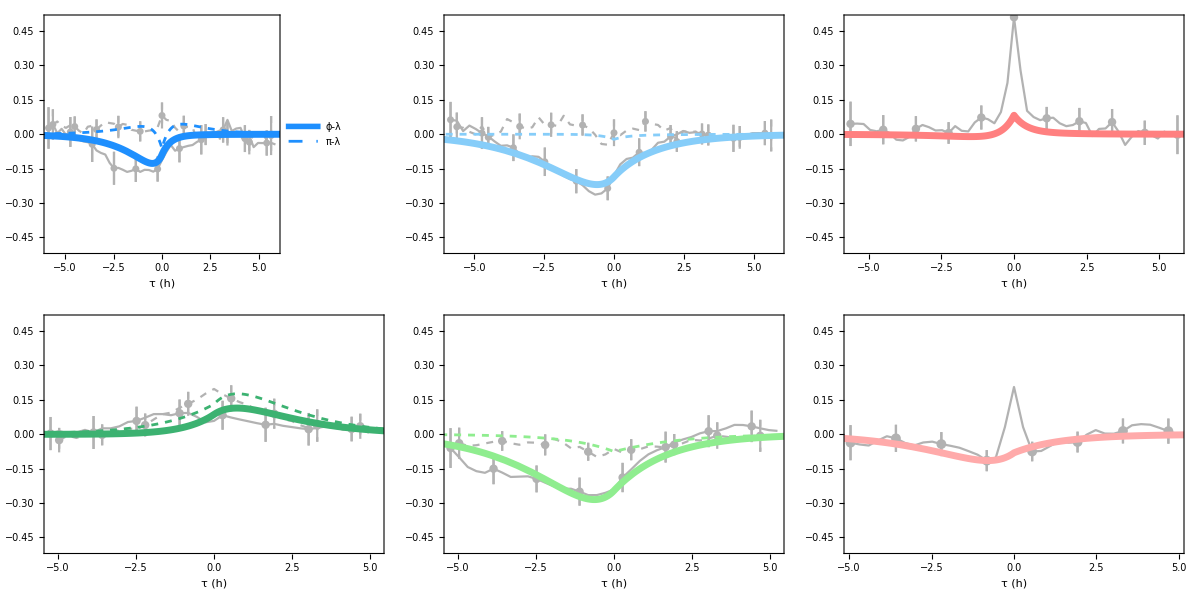

```mathematica
QuanFitPlot={{Plot[{ Rϕyλ[t]/.λR/.fitWT, Rπyλ[t]/.λR/.fitWT},{t,-10,10}, FrameLabel-> {{"Correlation","" },{"τ","WT - Y"}},PlotStyle-> {{RGBWTY,AbsoluteThickness[5]},{RGBWTY,AbsoluteThickness[2],Dashed}},PlotLegends->Placed[LineLegend[{"ϕ-λ","π-λ"},LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],{0.2,0.75}]],
Plot[{ Rϕhλ[t]/.λR/.fitWT, Rπhλ[t]/.λR/.fitWT},{t,-10,10}, FrameLabel-> {{"Correlation","" },{"τ","WT - H"}},PlotStyle-> {{RGBWTH,AbsoluteThickness[5]},{RGBWTH,AbsoluteThickness[2],Dashed}}],
Plot[ Rπhπy[t]/.λR/.fitWT,{t,-10,10}, FrameLabel-> {{"Correlation","" },{"τ","WT - π π"}},PlotStyle-> {{Pink,AbsoluteThickness[5]}}]},
{Plot[{ Rϕyλ[t]/.λR/.fitMUT, Rπyλ[t]/.λR/.fitMUT},{t,-10,10}, FrameLabel-> {{"Correlation","" },{"τ","MUT - Y"}},PlotStyle-> {{RGBMUTY,AbsoluteThickness[5]},{RGBMUTY,AbsoluteThickness[2],Dashed}}],
Plot[{ Rϕhλ[t]/.λR/.fitMUT, Rπhλ[t]/.λR/.fitMUT},{t,-10,10}, FrameLabel-> {{"Correlation","" },{"τ","MUT - H"}},PlotStyle-> {{RGBMUTH,AbsoluteThickness[5]},{RGBMUTH,AbsoluteThickness[2],Dashed}}],
Plot[Rπhπy[t]/.λR/.fitMUT,{t,-10,10}, FrameLabel-> {{"Correlation","" },{"τ","MUT - ππ"}},PlotStyle-> {{Lighter[Pink],AbsoluteThickness[5]}}]}};

diskr= Graphics[{Opacity[ 0.7],White,Disk[{0,0},20]}];
WTOPTMUTplot={{Show[YWTPlot,diskr,QuanFitPlot⟦1,1⟧],Show[HWTPlot,diskr,QuanFitPlot⟦1,2⟧],Show[ππWTPlot,diskr,QuanFitPlot⟦1,3⟧]},{Show[YOPTMUTPlot,diskr,QuanFitPlot⟦2,1⟧],Show[HOPTMUTPlot,diskr,QuanFitPlot⟦2,2⟧],Show[ππOPTMUTPlot,diskr,QuanFitPlot⟦2,3⟧]}}//TableForm
```

### Quantitatively Fitting Low and High Mutant Data

We show that the quantitative fits are not  much better than the qualitative fits, which are however easier to explain phenomenologically.

```mathematica
(*Fitting only LOW Mutant*)
λ0 =  1/2(0.37  +0.32); Clear[λR]; 
λR = {TMC-> TR+TMπ-TMλ,λE-> λ0(1-TCM(TR + TMπ-TMλ)),L-> -α1(TR +α2 TMπ), TMπh-> TMπ,θπc->0,βπc-> 1}; 

parMUT= {TR-> 0,TMλ-> TMλfit, TCM ->1, TMπ->TMπfit,α1-> αfit, α2-> 0,θπc-> 0,θπy-> θπyfit,θπh->θπhfit,θλ->θλfit,θs->1,θM-> θMfit,βπc-> 1,βπy-> βπ * λ0,βπh->  βπ * λ0,βλ-> βμ * λ0,βs-> βμ * λ0,βM-> βμ * λ0};
assumfit = {θπyfit>0,θπhfit>0,θλfit>0,θMfit>0, 5>βπ>1,βμ>0.5,-1<TMλfit<1,-1<TMπfit<1,1>αfit>0};

assumfit = {  0<θπyfit<2, 1.06< θπhfit< 1.24,θλfit== 0.143, 0.83<θMfit<0.97,1.8<βπ<2.16,0.75<βμ<.82,-1<TMλfit<1,-1<TMπfit<1, αfit ==0};
fit=NMinimize[{Total[Flatten[(# #)&/@{
(*Wild Type*)
(RϕYλLOWDATA⟦All,2⟧  - ((Rϕyλ[#]/.λR/.parMUT)&/@RϕYλLOWDATA⟦All,1⟧))/σϕYλLOWDATA,
(RπYλLOWDATA⟦All,2⟧  - ((Rπyλ[#]/.λR/.parMUT)&/@RπYλLOWDATA⟦All,1⟧))/σπYλLOWDATA,
(RϕHλLOWDATA⟦All,2⟧  - ((Rϕhλ[#]/.λR/.parMUT)&/@RϕHλLOWDATA⟦All,1⟧))/σϕHλLOWDATA,
(RπHλLOWDATA⟦All,2⟧  - ((Rπhλ[#]/.λR/.parMUT)&/@RπHλLOWDATA⟦All,1⟧))/σπHλLOWDATA
}]],assumfit},{TMλfit,TMπfit,αfit,θπyfit,θπhfit,θλfit,θMfit,βπ,βμ},MaxIterations->1000]
fitLOW = parMUT/.fit⟦2⟧;
```

{32.3899,{TMλfit→0.0739878,TMπfit→0.141894,αfit→0,θπyfit→2.,θπhfit→1.06,θλfit→0.143,θMfit→0.97,βπ→1.8,βμ→0.82}}

```mathematica
(*Fitting only HIGH Mutant*)
λ0 =1/2(0.58+0.62);Clear[λR];
λR = {TMC-> TR+TMπ-TMλ,λE-> λ0(1-TCM(TR + TMπ-TMλ)),L-> -α1(TR +α2 TMπ), TMπh-> TMπ,θπc->0,βπc-> 1}; 

parMUT= {TR-> 0,TMλ-> TMλfit, TCM ->1, TMπ->TMπfit,α1-> αfit, α2-> 0,θπc-> 0,θπy-> θπyfit,θπh->θπhfit,θλ->θλfit,θs->1,θM-> θMfit,βπc-> 1,βπy-> βπ * λ0,βπh->  βπ * λ0,βλ-> βμ * λ0,βs-> βμ * λ0,βM-> βμ * λ0};
assumfit = {   5>θπyfit>0,  5>θπhfit>0,  5>θλfit>0,   5>θMfit>0,5>βπ>2,βμ>0.5,-1<TMλfit<-0.5,-1<TMπfit<1,1>αfit>0};

assumfit = {  0<θπyfit<0.7, 1.06< θπhfit< 1.24,θλfit== 0.143, 0.83<θMfit<0.97,1.8<βπ<2.16,0.75<βμ<4,-1<TMλfit<-0.5,-1<TMπfit<1, αfit ==0};

fit=NMinimize[{Total[Flatten[(# #)&/@{
(*Wild Type*)
(RϕYλHIGHDATA⟦All,2⟧  - ((Rϕyλ[#]/.λR/.parMUT)&/@RϕYλHIGHDATA⟦All,1⟧))/σϕYλHIGHDATA,
(RπYλHIGHDATA⟦All,2⟧  - ((Rπyλ[#]/.λR/.parMUT)&/@RπYλHIGHDATA⟦All,1⟧))/σπYλHIGHDATA,
(RϕHλHIGHDATA⟦All,2⟧  - ((Rϕhλ[#]/.λR/.parMUT)&/@RϕHλHIGHDATA⟦All,1⟧))/σϕHλHIGHDATA,
(RπHλHIGHDATA⟦All,2⟧  - ((Rπhλ[#]/.λR/.parMUT)&/@RπHλHIGHDATA⟦All,1⟧))/σπHλHIGHDATA
}]],assumfit},{TMλfit,TMπfit,αfit,θπyfit,θπhfit,θλfit,θMfit,βπ,βμ},MaxIterations->1000]
fitHIGH = parMUT/.fit⟦2⟧;
```

{58.6118,{TMλfit→-0.770348,TMπfit→-0.316308,αfit→0,θπyfit→0.7,θπhfit→1.06,θλfit→0.143,θMfit→0.97,βπ→2.16,βμ→3.16141}}

```mathematica
fitHIGH = parMUT/.fit⟦2⟧;
```

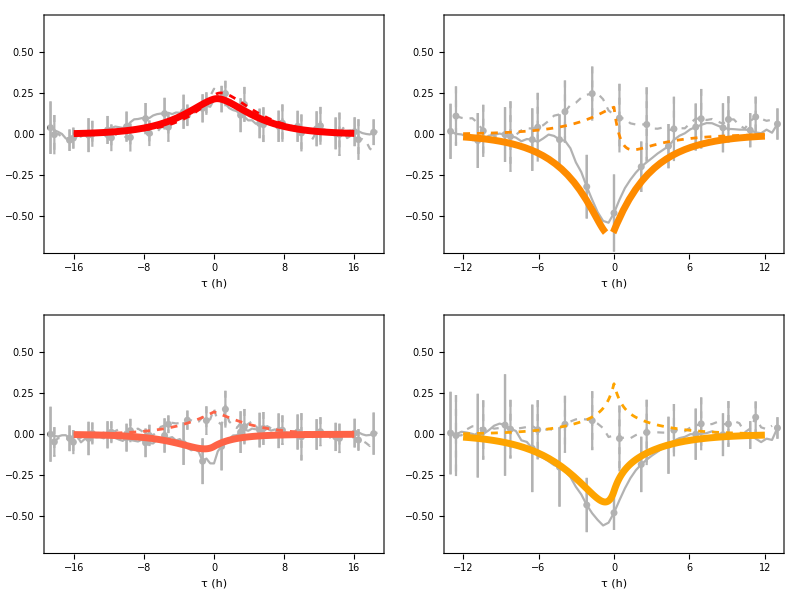

```mathematica
LOWHIGHMUTPLOT ={{Show[YMUTLOWPlot,diskr,Plot[{Rϕyλ[t]/.λR/.fitLOW,Rπyλ[t]/.λR/.fitLOW},{t,-16,16},PlotStyle-> {{RGBLOWY,AbsoluteThickness[5]},{AbsoluteThickness[2],RGBLOWY,Dashed}}]],
Show[HMUTLOWPlot,diskr,Plot[{Rϕhλ[t]/.λR/.fitLOW,Rπhλ[t]/.λR/.fitLOW},{t,-16,16},PlotStyle-> {{RGBLOWH,AbsoluteThickness[5]},{RGBLOWH,AbsoluteThickness[2],Dashed}}]]},
{Show[YMUTHIGHPlot,diskr,Plot[{Rϕyλ[t]/.λR/.fitHIGH,Rπyλ[t]/.λR/.fitHIGH},{t,-12,12},PlotStyle-> {{RGBHIGHY,AbsoluteThickness[5]},{AbsoluteThickness[2],RGBHIGHY,Dashed}}]],
Show[HMUTHIGHPlot,diskr,Plot[{Rϕhλ[t]/.λR/.fitHIGH,Rπhλ[t]/.λR/.fitHIGH},{t,-12,12},PlotStyle-> {{RGBHIGHH,AbsoluteThickness[5]},{RGBHIGHH,AbsoluteThickness[2],Dashed}}]]}}ᵀ//TableForm
```

## Parametric Sensitivity Tests (takes a long time to run)

#### Defining Sensitivity-test functions

```mathematica
nvalmax =22;

calcAllSSWT[repars_,parstodo_,λ0_,fchange_]:=Module[{itodopar,ipar,ival,parrepival,S0,SSipar,SS},
S0 =calcSSWT[repars,λ0];
SS={};
For[itodopar = 1,itodopar≤ Length[parstodo],itodopar++,{
ipar =parstodo⟦itodopar⟧;
SSipar ={};
For[ival = 0,ival≤ nvalmax,ival++,{
parrepival=repars;
parrepival⟦ipar⟧=parrepival⟦ipar⟧*((1-fchange)+2*fchange*ival/nvalmax);
AppendTo[SSipar,{(1-fchange+2*fchange*ival/nvalmax),calcSSWT[parrepival,λ0]/S0}];
}];
AppendTo[SS,SSipar];
}];
Return[SS]
];

calcSSWT[repars_,λ0_]:=Module[{parrep,SS,λR},
λR = {TMC-> TR+TMπ-TMλ,λE-> λ0(1-TCM(TR + TMπ-TMλ)),L-> -α1(TR +α2 TMπ), TMπh-> TMπ,θπc->0,βπc-> 1}; 
parrep = 
{TR-> repars⟦1⟧,TCM-> repars⟦2⟧,TMλ-> repars⟦3⟧, TMπ-> repars⟦4⟧,α1->repars⟦5⟧,α2->repars⟦6⟧,θπy->repars⟦7⟧,θπh->repars⟦8⟧,θλ-> repars⟦9⟧,θs->repars⟦10⟧,θM->repars⟦11⟧,βπy->repars⟦12⟧*λ0,βπh-> repars⟦12⟧*λ0,βλ->repars⟦13⟧*λ0,βs->repars⟦13⟧*λ0,βM-> repars⟦13⟧*λ0};

SS=Total[Flatten[(# #)&/@{
(RϕYλDATA⟦All,2⟧  - ((Rϕyλ[#]/.λR/.parrep)&/@RϕYλDATA⟦All,1⟧))/σϕYλDATA,
(RπYλDATA⟦All,2⟧  - ((Rπyλ[#]/.λR/.parrep)&/@RπYλDATA⟦All,1⟧))/σπYλDATA,
(RϕHλDATA⟦All,2⟧  - ((Rϕhλ[#]/.λR/.parrep)&/@RϕHλDATA⟦All,1⟧))/σϕHλDATA,
(RπHλDATA⟦All,2⟧  - ((Rπhλ[#]/.λR/.parrep)&/@RπHλDATA⟦All,1⟧))/σπHλDATA,

(*Mutant*)
(RϕYλOPTMUTDATA⟦All,2⟧  - ((Rϕyλ[#]/.λR/.TR->0 /.parrep)&/@RϕYλOPTMUTDATA⟦All,1⟧))/σϕYλOPTMUTDATA,
(RπYλOPTMUTDATA⟦All,2⟧  - ((Rπyλ[#]/.λR/.TR-> 0/.parrep)&/@RπYλOPTMUTDATA⟦All,1⟧))/σπYλOPTMUTDATA,
(RϕHλOPTMUTDATA⟦All,2⟧  - ((Rϕhλ[#]/.λR/.TR-> 0/.parrep)&/@RϕHλOPTMUTDATA⟦All,1⟧))/σϕHλOPTMUTDATA,
(RπHλOPTMUTDATA⟦All,2⟧  - ((Rπhλ[#]/.λR/.TR-> 0/.parrep)&/@RπHλOPTMUTDATA⟦All,1⟧))/σπHλOPTMUTDATA
}]];
Return[SS];
]

calcAllSSLOW[repars_,parstodo_,λ0_,fchange_]:=Module[{itodopar,ipar,ival,parrepival,S0,SSipar,SS},
S0 =calcSSLOW[repars,λ0];
SS={};
For[itodopar = 1,itodopar≤ Length[parstodo],itodopar++,{
ipar =parstodo⟦itodopar⟧;
SSipar ={};
For[ival = 0,ival≤ nvalmax,ival++,{
parrepival=repars;
parrepival⟦ipar⟧=parrepival⟦ipar⟧*((1-fchange)+2*fchange*ival/nvalmax);
AppendTo[SSipar,{(1-fchange+2*fchange*ival/nvalmax),calcSSLOW[parrepival,λ0]/S0}];
}];
AppendTo[SS,SSipar];
}];
Return[SS]
];


calcSSLOW[repars_,λ0_]:=Module[{parrep,SS,λR},
λR = {TMC-> TR+TMπ-TMλ,λE-> λ0(1-TCM(TR + TMπ-TMλ)),L-> -α1(TR +α2 TMπ), TMπh-> TMπ,θπc->0,βπc-> 1}; 
parrep = {TR-> repars⟦1⟧,TCM-> repars⟦2⟧,TMλ-> repars⟦3⟧, TMπ-> repars⟦4⟧,α1->repars⟦5⟧,α2->repars⟦6⟧,θπy->repars⟦7⟧,θπh->repars⟦8⟧,θλ-> repars⟦9⟧,θs->repars⟦10⟧,θM->repars⟦11⟧,βπy->repars⟦12⟧*λ0,βπh-> repars⟦12⟧*λ0,βλ->repars⟦13⟧*λ0,βs->repars⟦13⟧*λ0,βM-> repars⟦13⟧*λ0};
SS=Total[Flatten[(# #)&/@{
(RϕYλLOWDATA⟦All,2⟧  - ((Rϕyλ[#]/.λR/.TR->0/.parrep)&/@RϕYλLOWDATA⟦All,1⟧))/σϕYλLOWDATA,
(RπYλLOWDATA⟦All,2⟧  - ((Rπyλ[#]/.λR/.TR->0/.parrep)&/@RπYλLOWDATA⟦All,1⟧))/σπYλLOWDATA,
(RϕHλLOWDATA⟦All,2⟧  - ((Rϕhλ[#]/.λR/.TR->0/.parrep)&/@RϕHλLOWDATA⟦All,1⟧))/σϕHλLOWDATA,
(RπHλLOWDATA⟦All,2⟧  - ((Rπhλ[#]/.λR/.TR->0/.parrep)&/@RπHλLOWDATA⟦All,1⟧))/σπHλLOWDATA,
0.0(RπHπYLOWDATA⟦All,2⟧  - ((Rπhπy[#]/.parrep)&/@RπHπYLOWDATA⟦All,1⟧))/σπHπYLOWDATA
}]];
Return[SS];
];



calcAllSSHIGH[repars_,parstodo_,λ0_,fchange_]:=Module[{itodopar,ipar,ival,parrepival,S0,SSipar,SS},
S0 =calcSSHIGH[repars,λ0];
SS={};
For[itodopar = 1,itodopar≤ Length[parstodo],itodopar++,{
ipar =parstodo⟦itodopar⟧;
SSipar ={};
For[ival = 0,ival≤ nvalmax,ival++,{
parrepival=repars;
parrepival⟦ipar⟧=parrepival⟦ipar⟧*((1-fchange)+2*fchange*ival/nvalmax);
AppendTo[SSipar,{(1-fchange+2*fchange*ival/nvalmax),calcSSHIGH[parrepival,λ0]/S0}];
}];
AppendTo[SS,SSipar];
}];
Return[SS]
];

calcSSHIGH[repars_,λ0_]:=Module[{parrep,SS,λR},
λR = {TMC-> TR+TMπ-TMλ,λE-> λ0(1-TCM(TR + TMπ-TMλ)),L-> -α1(TR +α2 TMπ), TMπh-> TMπ,θπc->0,βπc-> 1}; 
parrep = {TR-> repars⟦1⟧,TCM-> repars⟦2⟧,TMλ-> repars⟦3⟧, TMπ-> repars⟦4⟧,α1->repars⟦5⟧,α2->repars⟦6⟧,θπy->repars⟦7⟧,θπh->repars⟦8⟧,θλ-> repars⟦9⟧,θs->repars⟦10⟧,θM->repars⟦11⟧,βπy->repars⟦12⟧*λ0,βπh-> repars⟦12⟧*λ0,βλ->repars⟦13⟧*λ0,βs->repars⟦13⟧*λ0,βM-> repars⟦13⟧*λ0};
SS=Total[Flatten[(# #)&/@{
(*Mutant*)
(RϕYλHIGHDATA⟦All,2⟧  - ((Rϕyλ[#]/.λR/.TR->0/.parrep)&/@RϕYλHIGHDATA⟦All,1⟧))/σϕYλHIGHDATA,
(RπYλHIGHDATA⟦All,2⟧  - ((Rπyλ[#]/.λR/.TR->0/.parrep)&/@RπYλHIGHDATA⟦All,1⟧))/σπYλHIGHDATA,
(RϕHλHIGHDATA⟦All,2⟧  - ((Rϕhλ[#]/.λR/.TR->0/.parrep)&/@RϕHλHIGHDATA⟦All,1⟧))/σϕHλHIGHDATA,
(RπHλHIGHDATA⟦All,2⟧  - ((Rπhλ[#]/.λR/.TR->0/.parrep)&/@RπHλHIGHDATA⟦All,1⟧))/σπHλHIGHDATA,
0.0(RπHπYHIGHDATA⟦All,2⟧  - ((Rπhπy[#]/.parrep)&/@RπHπYHIGHDATA⟦All,1⟧))/σπHπYHIGHDATA
}]];
Return[SS];
]
```

#### Calculating critical SS value from F-statistics

```mathematica
dfWT = 4*Length[RϕYλDATA] +4*Length[RϕYλOPTMUTDATA]- Length[{"TR", "TMλ","TMπ","α1","θπy","θπh","θλ","θM","βπ", "βμ"}]
dfLOW = 4*Length[RϕYλLOWDATA] - Length[{"TR", "TMλ","TMπ","α1","θπy","θπh","θλ","θM","βπ", "βμ"}]
dfHIGH = 4*Length[RϕYλHIGHDATA] - Length[{"TR", "TMλ","TMπ","α1","θπy","θπh","θλ","θM","βπ", "βμ"}]
```

6

-2

-2

```mathematica
FcritWT = 3.89; (*From F-table*)
FcritLOW = 3.89;
FcritHIGH = 3.89;
```

```mathematica
SSmaxoverSS0[df_,Fcrit_]:=(df+Fcrit)/df
```

#### Declaring Best Fits

Best Fits are declared here:

```mathematica
λ0 = 0.795;
fitparWT={TR,TCM,TMλ,TMπ,α1,α2,θπy,θπh,θλ,θs,θM,βπy/λ0,βλ/λ0} /.fitWT

λ0=(0.37  +0.32)/2;
fitparLOW = {TR,TCM,TMλ,TMπ,α1,α2,θπy,θπh,θλ,θs,θM,βπy/λ0,βλ/λ0} /.fitLOW


λ0 = (0.58+0.62)/2;
fitparHIGH ={TR,TCM,TMλ,TMπ,α1,α2,θπy,θπh,θλ,θs,θM,βπy/λ0,βλ/λ0} /.fitHIGH

fitparHIGH ={TR,TCM,TMλ,TMπ,α1,α2,θπy,θπh,θλ,θs,1,βπy/λ0,βλ/λ0} /.fitHIGH
```

ReplaceAll::reps: {TRfit,TMλfit,TMπfit,αfit,θπyfit,θπhfit,θλfit,θMfit,βπ,βμ} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{TR→TRfit,TMλ→TMλfit,TCM→1,TMπ→TMπfit,α1→αfit,α2→0,θπy→θπyfit,θπh→θπhfit,θλ→θλfit,θs→1,«6»}/.{TRfit,TMλfit,TMπfit,αfit,θπyfit,θπhfit,θλfit,θMfit,βπ,βμ}} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{TR,TCM,TMλ,TMπ,α1,α2,θπy,θπh,θλ,θs,θM,1.25786 βπy,1.25786 βλ}/.({TR→TRfit,TMλ→TMλfit,TCM→1,TMπ→TMπfit,α1→αfit,α2→0,θπy→θπyfit,θπh→θπhfit,θλ→θλfit,θs→1,θM→θMfit,βπy→0.795 βπ,βπh→0.795 βπ,βλ→0.795 βμ,βs→0.795 βμ,βM→0.795 βμ}/.{TRfit,TMλfit,TMπfit,αfit,θπyfit,θπhfit,θλfit,θMfit,βπ,βμ})

ReplaceAll::reps: {{TR→0,TMλ→TMλfit,TCM→1,TMπ→TMπfit,α1→αfit,α2→0,θπc→0,θπy→θπyfit,θπh→θπhfit,θλ→θλfit,«8»}/.{TMλfit,TMπfit,αfit,θπyfit,θπhfit,θλfit,θMfit,βπ,βμ}} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{TR,TCM,TMλ,TMπ,α1,α2,θπy,θπh,θλ,θs,θM,2.89855 βπy,2.89855 βλ}/.({TR→0,TMλ→TMλfit,TCM→1,TMπ→TMπfit,α1→αfit,α2→0,θπc→0,θπy→θπyfit,θπh→θπhfit,θλ→θλfit,θs→1,θM→θMfit,βπc→1,βπy→0.345 βπ,βπh→0.345 βπ,βλ→0.345 βμ,βs→0.345 βμ,βM→0.345 βμ}/.{TMλfit,TMπfit,αfit,θπyfit,θπhfit,θλfit,θMfit,βπ,βμ})

ReplaceAll::reps: {{TR→0,TMλ→TMλfit,TCM→1,TMπ→TMπfit,α1→αfit,α2→0,θπc→0,θπy→θπyfit,θπh→θπhfit,θλ→θλfit,«8»}/.{TMλfit,TMπfit,αfit,θπyfit,θπhfit,θλfit,θMfit,βπ,βμ}} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{TR,TCM,TMλ,TMπ,α1,α2,θπy,θπh,θλ,θs,θM,1.66667 βπy,1.66667 βλ}/.({TR→0,TMλ→TMλfit,TCM→1,TMπ→TMπfit,α1→αfit,α2→0,θπc→0,θπy→θπyfit,θπh→θπhfit,θλ→θλfit,θs→1,θM→θMfit,βπc→1,βπy→0.6 βπ,βπh→0.6 βπ,βλ→0.6 βμ,βs→0.6 βμ,βM→0.6 βμ}/.{TMλfit,TMπfit,αfit,θπyfit,θπhfit,θλfit,θMfit,βπ,βμ})

ReplaceAll::reps: {{TR→0,TMλ→TMλfit,TCM→1,TMπ→TMπfit,α1→αfit,α2→0,θπc→0,θπy→θπyfit,θπh→θπhfit,θλ→θλfit,«8»}/.{TMλfit,TMπfit,αfit,θπyfit,θπhfit,θλfit,θMfit,βπ,βμ}} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{TR,TCM,TMλ,TMπ,α1,α2,θπy,θπh,θλ,θs,1,1.66667 βπy,1.66667 βλ}/.({TR→0,TMλ→TMλfit,TCM→1,TMπ→TMπfit,α1→αfit,α2→0,θπc→0,θπy→θπyfit,θπh→θπhfit,θλ→θλfit,θs→1,θM→θMfit,βπc→1,βπy→0.6 βπ,βπh→0.6 βπ,βλ→0.6 βμ,βs→0.6 βμ,βM→0.6 βμ}/.{TMλfit,TMπfit,αfit,θπyfit,θπhfit,θλfit,θMfit,βπ,βμ})

```mathematica
{0,1,-0.6729277592843093,-0.4754361912610345,0.,0,4.999999971207562,4.791707759043907,2.498328658133171,1,..`,2.478844451513981,1.8175312965673494}
```

#### Calculate Sensitivities

Calculate and plot Sensitivities:

```mathematica
SetOptions[ListPlot,{PlotRange->{All,{0.98,1.05}},PlotStyle-> {{AbsoluteThickness[3],Dashed}},Frame-> True,FrameStyle-> Thick,LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],ImageSize-> 500,Joined->True,Mesh->All,MeshStyle-> Black,FrameLabel-> {"p/p^*","SS/SS^*"}} ];
SetOptions[Plot,{PlotRange->{All,{0.98,1.05}},PlotStyle->{{Black,AbsoluteThickness[5]}}}];
```

For the WildType and Optimal Mutants:

```mathematica
Clear[λ0];
λ0 = 0.795;
plotpars = Table[i,{i,1,13}];  (*Elements of: {"TR", "TMC","TMλ","TMπ", "α1","α2", "θπy","θπh","θλ", "θs","θM","βπ", "βμ"}*)
fitparWT (*Check parameters*)
```

{TR,TCM,TMλ,TMπ,α1,α2,θπy,θπh,θλ,θs,θM,1.25786 βπy,1.25786 βλ}/.({TR→TRfit,TMλ→TMλfit,TCM→1,TMπ→TMπfit,α1→αfit,α2→0,θπy→θπyfit,θπh→θπhfit,θλ→θλfit,θs→1,θM→θMfit,βπy→0.795 βπ,βπh→0.795 βπ,βλ→0.795 βμ,βs→0.795 βμ,βM→0.795 βμ}/.{TRfit,TMλfit,TMπfit,αfit,θπyfit,θπhfit,θλfit,θMfit,βπ,βμ})

```mathematica
SSWT=calcAllSSWT[fitparWT,plotpars,λ0,0.3];
```

Part::partw: Part 3 of {TR,TCM,TMλ,TMπ,α1,α2,θπy,θπh,θλ,θs,«3»}/.({TR→TRfit,TMλ→TMλfit,TCM→1,TMπ→TMπfit,α1→αfit,α2→0,θπy→θπyfit,θπh→θπhfit,θλ→θλfit,θs→1,«6»}/.{TRfit,TMλfit,TMπfit,αfit,θπyfit,θπhfit,θλfit,θMfit,βπ,βμ}) does not exist.

Part::partw: Part 4 of {TR,TCM,TMλ,TMπ,α1,α2,θπy,θπh,θλ,θs,«3»}/.({TR→TRfit,TMλ→TMλfit,TCM→1,TMπ→TMπfit,α1→αfit,α2→0,θπy→θπyfit,θπh→θπhfit,θλ→θλfit,θs→1,«6»}/.{TRfit,TMλfit,TMπfit,αfit,θπyfit,θπhfit,θλfit,θMfit,βπ,βμ}) does not exist.

Part::partw: Part 5 of {TR,TCM,TMλ,TMπ,α1,α2,θπy,θπh,θλ,θs,«3»}/.({TR→TRfit,TMλ→TMλfit,TCM→1,TMπ→TMπfit,α1→αfit,α2→0,θπy→θπyfit,θπh→θπhfit,θλ→θλfit,θs→1,«6»}/.{TRfit,TMλfit,TMπfit,αfit,θπyfit,θπhfit,θλfit,θMfit,βπ,βμ}) does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {{}} + {-Divide[Divide[-0.5 <<1>> Piecewise[{{Divide[1, Power[E, 0.795 $Failed ({TR, TCM, TMλ, <<9>>, 1.25786 βλ} /. <<1>>)[[13]]] (0.795 + <<1>>)], <<1>>}, {<<2>>}}], <<1>>] + <<4>>, <<1>>], <<12>>} cannot be combined.

Thread::tdlen: Objects of unequal length in {{{}} + {-Divide[Divide[-0.5 <<1>> Piecewise[{{Divide[1, Power[E, 0.795 <<2>>] (0.795 + 0.795 ({TR, <<12>>} /. <<1>>)[[13]])], <<1>>}, {<<2>>}}], <<1>>] + <<4>>, Power[<<2>>]], <<12>>}, {<<13>>}} {<<1>>} cannot be combined.

Thread::tdlen: Objects of unequal length in {{}} + {-Divide[Divide[0.628931 <<2>> Power[({TR, TCM, TMλ, TMπ, α1, α2, θπy, θπh, θλ, θs, θM, 1.25786 βπy, 1.25786 βλ} /. ({<<16>>} /. {<<10>>}))[[11]], 2], <<1>>] + <<3>>, Power[<<2>>]], <<11>>, -<<1>>} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

ReplaceAll::reps: {{TR→TRfit,TMλ→TMλfit,TCM→1,TMπ→TMπfit,α1→αfit,α2→0,θπy→θπyfit,θπh→θπhfit,θλ→θλfit,θs→1,«6»}/.{TRfit,TMλfit,TMπfit,αfit,θπyfit,θπhfit,θλfit,θMfit,βπ,βμ}} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::partw: Part 3 of {TR,TCM,TMλ,TMπ,α1,α2,θπy,θπh,θλ,θs,«3»}/.({TR→TRfit,TMλ→TMλfit,TCM→1,TMπ→TMπfit,α1→αfit,α2→0,θπy→θπyfit,θπh→θπhfit,θλ→θλfit,θs→1,«6»}/.{TRfit,TMλfit,TMπfit,αfit,θπyfit,θπhfit,θλfit,θMfit,βπ,βμ}) does not exist.

General::stop: Further output of Set::partw will be suppressed during this calculation.

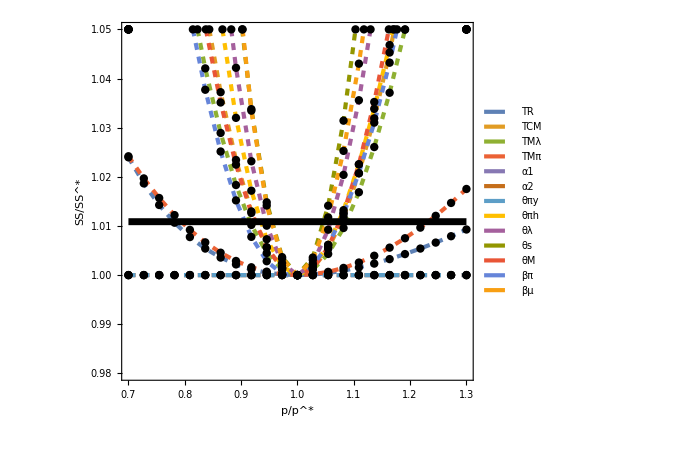

```mathematica
Show[ListPlot[SSWT,PlotLegends->{"TR", "TCM","TMλ","TMπ", "α1","α2", "θπy","θπh","θλ", "θs","θM","βπ", "βμ"}⟦plotpars⟧],Plot[SSmaxoverSS0[dfWT,FcritWT],{x,0.7,1.3}]]
```

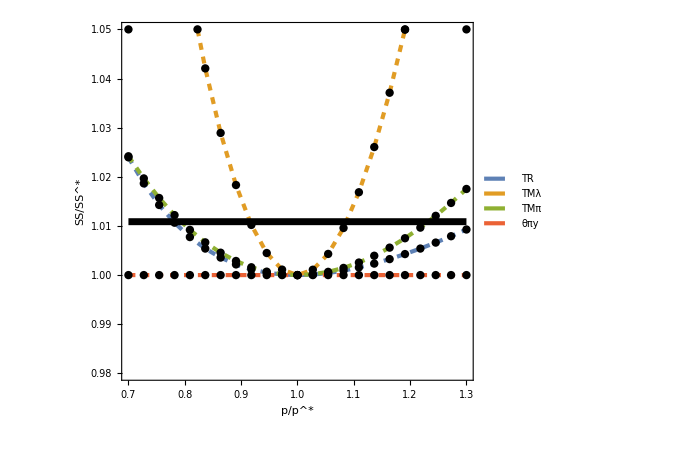

```mathematica
plotpars = {1,3,4,7};
Show[ListPlot[SSWT⟦plotpars⟧,PlotLegends->{"TR", "TCM","TMλ","TMπ", "α1","α2", "θπy","θπh","θλ", "θs","θM","βπ", "βμ"}⟦plotpars⟧],Plot[SSmaxoverSS0[dfWT,FcritWT],{x,0.7,1.3}]]
```

Further calculating the confidence range of each parameter

```mathematica
λ0 = 0.795;
fitparWT={TR,TCM,TMλ,TMπ,α1,α2,θπy,θπh,θλ,θs,θM,βπy/λ0,βλ/λ0} /.fitWT

par = 12;
SSWT=calcAllSSWT[fitparWT,{par},λ0,0.1];
SS= {SSWT⟦1,All,1⟧,SSWT⟦1,All,2⟧-SSmaxoverSS0[dfWT,FcritWT]}ᵀ
```

{-1.67303,1,0.05004,-0.178541,1.04256×10^-11,0,0.0000530155,1.14419,0.134017,1,0.899988,2.,0.780787}

{{0.9,0.00157951},{0.909091,-0.000891855},{0.918182,-0.00308704},{0.927273,-0.00500882},{0.936364,-0.00665993},{0.945455,-0.0080431},{0.954545,-0.00916104},{0.963636,-0.0100164},{0.972727,-0.010612},{0.981818,-0.0109503},{0.990909,-0.0110341},{1.,-0.0108659},{1.00909,-0.0104484},{1.01818,-0.00978415},{1.02727,-0.00887571},{1.03636,-0.00772566},{1.04545,-0.00633652},{1.05455,-0.00471083},{1.06364,-0.00285109},{1.07273,-0.000759798},{1.08182,0.00156057},{1.09091,0.00410756},{1.1,0.00687872}}

```mathematica
fitparWT⟦par⟧{SS⟦1,1⟧, SS⟦-6,1⟧}
```

{1.8,2.10909}

#### Low and high

For the LOW Mutant:

```mathematica
λ0=(0.37  +0.32)/2;
plotpars = {5,7,8};
SSLOW =calcAllSSLOW[fitparLOW,plotpars,λ0,0.2];
```

```mathematica
fitparLOW
```

{0,1,0.860396,0.672941,0.0570264,0,9.21024,8.27692,9.03025×10^-9,1,0.641188,4.21106,0.976587}

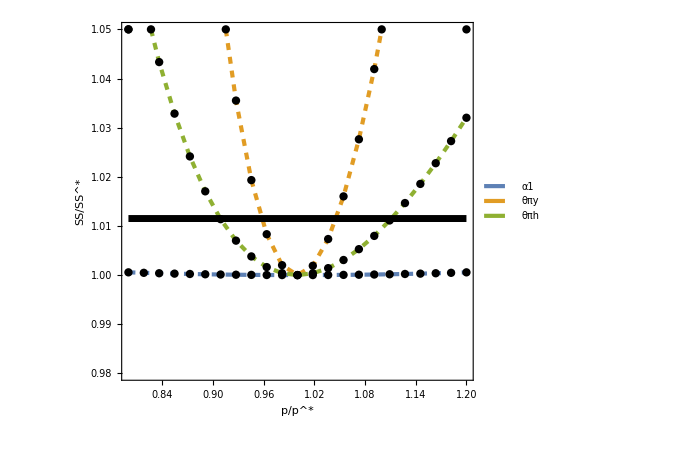

```mathematica
Show[ListPlot[SSLOW,PlotLegends->{"TR", "TCM","TMλ","TMπ", "α1","α2", "θπy","θπh","θλ", "θs","θM","βπ", "βμ"}⟦plotpars⟧ ],Plot[SSmaxoverSS0[dfLOW,FcritLOW],{x,0.8,1.2}]]
```

For the HIGH Mutant:

```mathematica
λ0 = (0.58+0.62)/2;
plotpars = {3,4,7,8,11,12,13};
fitparHIGH
SSHIGH = calcAllSSHIGH[fitparHIGH,plotpars,λ0,0.3];
```

{0,1,-0.672928,-0.475436,0.,0,5.,4.79171,2.49833,1,1,2.47884,1.81753}

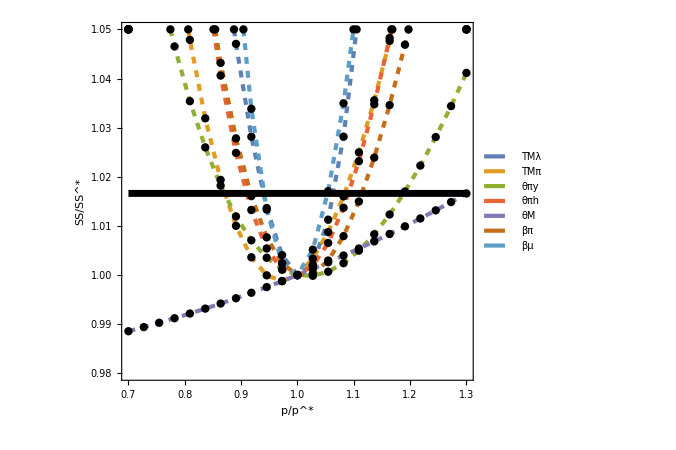

```mathematica
Show[ListPlot[SSHIGH,Joined-> True,PlotLegends-> {"TR", "TCM","TMλ","TMπ", "α1", "α2","θπy","θπh","θλ", "θs","θM","βπ", "βμ"}⟦plotpars⟧],Plot[SSmaxoverSS0[dfHIGH,FcritHIGH],{x,0.7,1.3}]]
```

## Qualitative Parameter Fits and Plots

The parameter L reflects an extension of the model that sets the direct competition (e.g for ribosomes) between the production rates. It is set to zero always.
Here, we start from the best-fitted parameters and first adjust parameters within their confidence range (determined with the sensitivity analysis above) to a fit that is nice for the eyes.  We show that, to some extent, these parameters also  predict the πH-πY cross-correlations under the assumption that the measured cross-correlations strongly overshoot at zero delay.

Next, we tune the parameters to create the plots for the Low and High mutants which are shown in the main text.

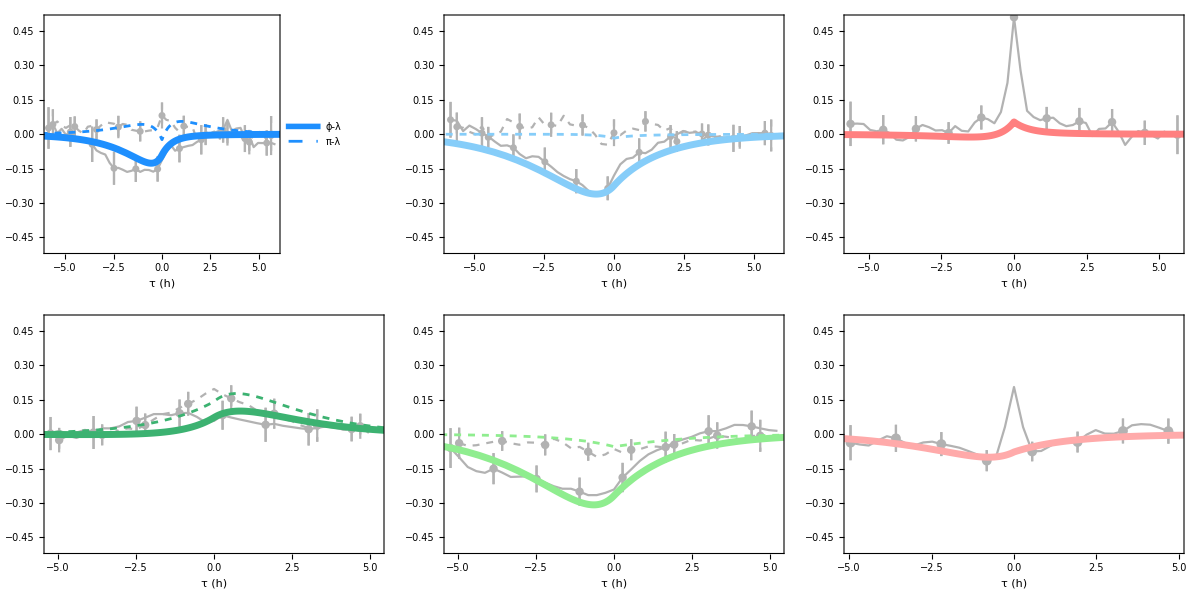

```mathematica
(*best qualitative fit parameters*)
λ0 = 0.795; Clear[λR];
λR = {TMC-> TR+TMπ-TMλ,λE-> λ0(1-TCM(TR + TMπ-TMλ)),L-> -α1(TR +α2 TMπ), TMπh-> TMπ,θπc->0,βπc-> 1}; 

(* mathematically equivalent to: *)
allparams = {TR-> TRval,TCM-> 1,TMλ-> 0.05, TMπ-> -0.13,α1-> 0,α2->0,θπy-> 0.1,θπh->1.14,θλ-> 0.15,θs->1,θM-> 0.9,βπy-> 2*λ0,βπh-> 2*λ0,βλ-> 0.7*λ0,βs-> 0.7*λ0,βM-> 0.7*λ0};  

repWT = allparams/.TRval -> -1.3;
repMUT = allparams/.TRval -> 0;

QualFitPlot={{Plot[{ Rϕyλ[t]/.λR/.repWT, Rπyλ[t]/.λR/.repWT},{t,-10,10}, FrameLabel-> {{"Correlation","" },{"τ","WT - Y"}},PlotStyle-> {{RGBWTY,AbsoluteThickness[5]},{RGBWTY,AbsoluteThickness[2],Dashed}},PlotLegends->Placed[LineLegend[{"ϕ-λ","π-λ"},LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],{0.2,0.75}]],
Plot[{ Rϕhλ[t]/.λR/.repWT, Rπhλ[t]/.λR/.repWT},{t,-10,10}, FrameLabel-> {{"Correlation","" },{"τ","WT - H"}},PlotStyle-> {{RGBWTH,AbsoluteThickness[5]},{RGBWTH,AbsoluteThickness[2],Dashed}}],
Plot[ Rπhπy[t]/.λR/.repWT,{t,-10,10}, FrameLabel-> {{"Correlation","" },{"τ","WT - ππ "}},PlotStyle-> {{Pink,AbsoluteThickness[5]},{Pink,AbsoluteThickness[2],Dashed}}]},
{Plot[{ Rϕyλ[t]/.λR/.repMUT, Rπyλ[t]/.λR/.repMUT},{t,-10,10}, FrameLabel-> {{"Correlation","" },{"τ","MUT - Y"}},PlotStyle-> {{RGBMUTY,AbsoluteThickness[5]},{RGBMUTY,AbsoluteThickness[2],Dashed}}],
Plot[{ Rϕhλ[t]/.λR/.repMUT, Rπhλ[t]/.λR/.repMUT},{t,-10,10}, FrameLabel-> {{"Correlation","" },{"τ","MUT - H"}},PlotStyle-> {{RGBMUTH,AbsoluteThickness[5]},{RGBMUTH,AbsoluteThickness[2],Dashed}}],
Plot[ Rπhπy[t]/.λR/.repMUT,{t,-10,10}, FrameLabel-> {{"Correlation","" },{"τ","MUT - ππ "}},PlotStyle-> {{Lighter[Pink],AbsoluteThickness[5]},{Lighter[Pink],AbsoluteThickness[2],Dashed}}]}};
diskr= Graphics[{Opacity[ 0.7],White,Disk[{0,0},19]}];

Comparisonplot={{Show[YWTPlot,diskr,QualFitPlot⟦1,1⟧],Show[HWTPlot,diskr,QualFitPlot⟦1,2⟧],Show[ππWTPlot,diskr,QualFitPlot⟦1,3⟧]},{Show[YOPTMUTPlot,diskr,QualFitPlot⟦2,1⟧],Show[HOPTMUTPlot,diskr,QualFitPlot⟦2,2⟧],Show[ππOPTMUTPlot,diskr,QualFitPlot⟦2,3⟧]}}//TableForm
```

#### LOW MUTANT: Qualitative fit

Qualitatively best fits for the LOW MUTANT (changing only transfer parameters and reporter noise amplitudes)

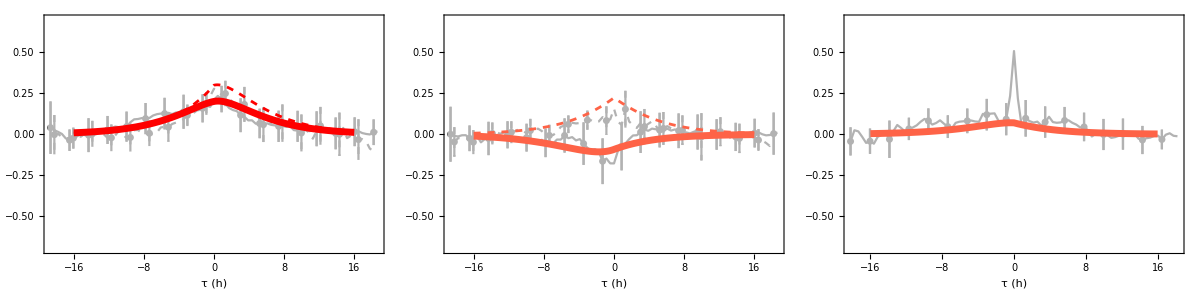

```mathematica
λ0 =  1/2(0.37  +0.32); Clear[λR]; 
λR = {TMC-> TR+TMπ-TMλ,λE-> λ0(1-TCM(TR + TMπ-TMλ)),L-> -α1(TR +α2 TMπ), TMπh-> TMπ,θπc->0,βπc-> 1}; 
repMUTLOW = {TR-> 0,TCM->1,TMλ-> .6, TMπ->0.45,α1-> 0,α2->0,θπy->5,θπh->3.5,θλ-> 0.15,θs->1,θM-> .9,βπy->2*λ0,βπh-> 2*λ0,βλ-> 0.7*λ0,βs-> 0.7*λ0,βM-> 0.7*λ0};  

LOWMUTPLOT ={{Show[YMUTLOWPlot,diskr,Plot[{Rϕyλ[t]/.λR/.repMUTLOW,Rπyλ[t]/.λR/.repMUTLOW},{t,-16,16},PlotStyle-> {{RGBLOWY,AbsoluteThickness[5]},{AbsoluteThickness[2],RGBLOWY,Dashed}}]],
Show[HMUTLOWPlot,diskr,Plot[{Rϕhλ[t]/.λR/.repMUTLOW,Rπhλ[t]/.λR/.repMUTLOW},{t,-16,16},PlotStyle-> {{RGBLOWH,AbsoluteThickness[5]},{RGBLOWH,AbsoluteThickness[2],Dashed}}]],Show[ππMUTLOWPlot,diskr,Plot[Rπhπy[t]/.λR/.repMUTLOW,{t,-16,16},PlotStyle-> {{RGBLOWH,AbsoluteThickness[5]},{RGBLOWH,AbsoluteThickness[2],Dashed}}]]}}//TableForm
```

#### HIGH MUTANT : Qualitative fit

Qualitative fits for HIGH mutant, changing transfer parameters, noise amplitudes and timescales of growth-related noise sources

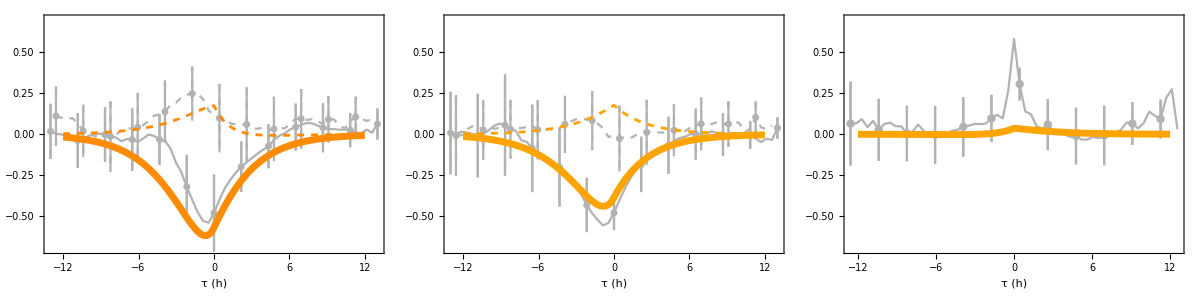

```mathematica
λ0 =(0.58+0.62)/2;Clear[λR];
λR = {TMC-> TR+TMπ-TMλ,λE-> λ0(1-TCM(TR + TMπ-TMλ)),L-> -α1(TR +α2 TMπ), TMπh-> TMπ,θπc->0,βπc-> 1}; 
repMUTHIGH = {TR-> 0,TCM-> 1,TMλ-> -0.6, TMπ-> -0.25,α1-> 00,α2->0,θπy->2.5,θπh->4,θλ-> 0.8,θs->1,θM->1.8,βπy-> 2*λ0,βπh-> 2*λ0,βλ->1.1*λ0,βs-> 1.2*λ0,βM-> 1.2*λ0};  
HIGHMUTPLOT = {{Show[YMUTHIGHPlot,diskr,Plot[{Rϕyλ[t]/.λR/.repMUTHIGH,Rπyλ[t]/.λR/.repMUTHIGH},{t,-12,12},PlotStyle-> {{RGBHIGHY,AbsoluteThickness[5]},{AbsoluteThickness[2],RGBHIGHY,Dashed}},PlotRange-> All]],
Show[HMUTHIGHPlot,diskr,Plot[{Rϕhλ[t]/.λR/.repMUTHIGH,Rπhλ[t]/.λR/.repMUTHIGH},{t,-12,12},PlotStyle-> {{RGBHIGHH,AbsoluteThickness[5]},{RGBHIGHH,AbsoluteThickness[2],Dashed}}]],Show[ππMUTHIGHPlot,diskr,Plot[Rπhπy[t]/.λR/.repMUTHIGH,{t,-12,12},PlotStyle-> {{RGBHIGHH,AbsoluteThickness[5]},{RGBHIGHH,AbsoluteThickness[2],Dashed}}]]}}//TableForm
```